```mathematica
ClearAll["Global`*"]
```

```mathematica
knots[[0]]
```

List

```mathematica
ToExpression[Import["/tmp/nurbs_eval.txt","String"]]
GraphicsGrid[Table[Table[
Show[{
Plot[
D[BSplineBasis[{p,knots},i,x],{x,k}]/.x->xx,{xx,knots[[1]],knots[[numKnots-p]]},
PlotStyle->Red,
PlotLabel->Subscript[funcN, ip]^k,
PlotRange->Full],
ListPlot[nn[i,p,k]]
}]
,{i,0,numKnots-p-2}],{k,0,1}]
]
```

-Graphics-

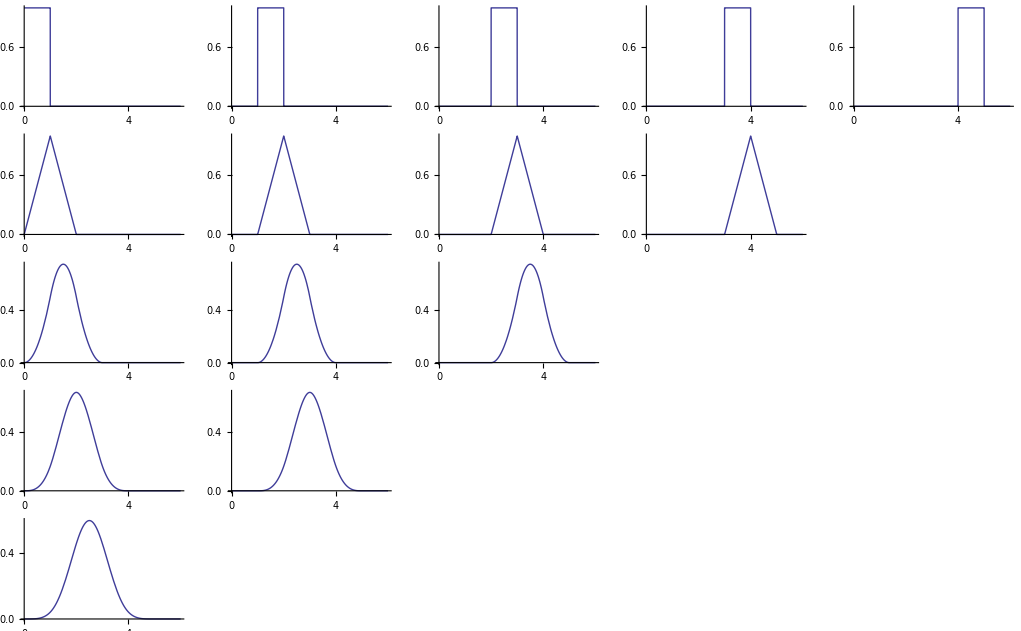

```mathematica
opp=5; knots=Table[i-1,{i,opp+1}];
GraphicsGrid[Table[Table[
Plot[BSplineBasis[{d,knots},i,x],{x,0,opp+1}]
,{i,0,opp-d-1}],{d,0,opp-1}]]
```